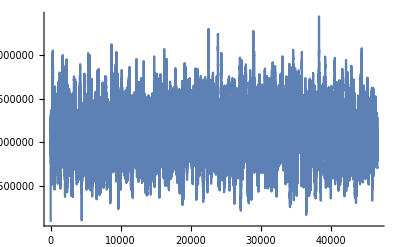
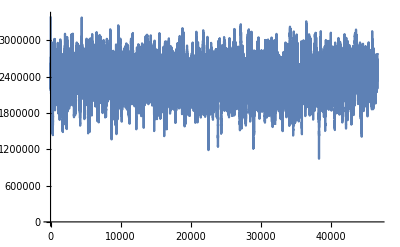
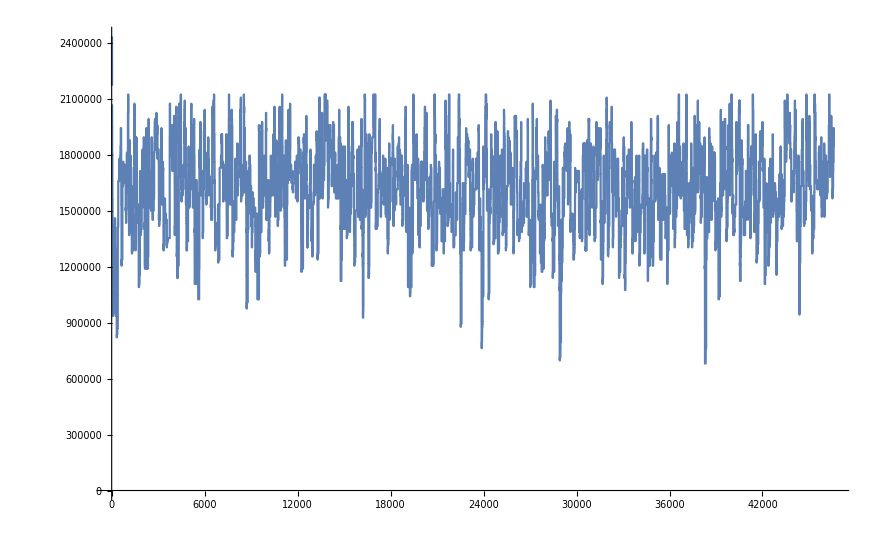
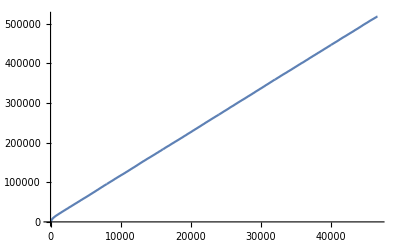
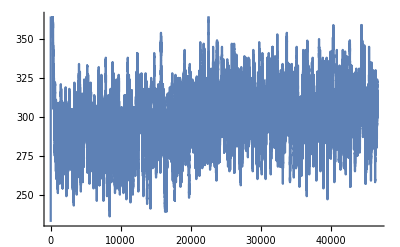

```mathematica
filename="d:/temp/out4.txt";
lines=Replace[#," "->""]&/@ReadList[filename,String];
rows=#[[1;;9]]&/@Partition[lines,10];
t=Map[Read[StringToStream[#]]&,Prepend[Last[StringSplit[#,"="]]&/@Rest[#],Last[StringSplit[First[#],{"#",":"}]]]&/@rows,{2}];
(* Grid[Take[t,10]] *)
ListLinePlot/@Transpose[{{#[[1]],#[[3]]},{#[[1]],#[[4]]},{#[[1]],#[[7]]},{#[[1]],#[[8]]},{#[[1]],#[[9]]}}&/@t]
(* 
allocated byte, available bytes, max free bLock size, merged blocks count, curr free blocks count 
*)
```

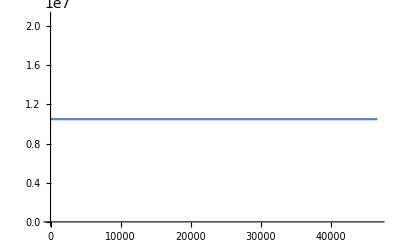
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot/@Transpose[{{#[[1]],#[[3]]},{#[[1]],#[[4]]},{#[[1]],#[[4]]+#[[3]]}}&/@t]
```